```mathematica
(*Directional Coupler Inital Parameters Coiuple Mode Theory *)
chi[vn_]:= Sqrt[3.]/2. Pi vn
db[z_]:=Pi Exp[-kpa( z)]
pltsph=ParametricPlot3D[{Cos[t] Cos[u], Sin[t] Cos[u],Sin[u]},{t,0.,2Pi},{u,-Pi/2,Pi/2},DisplayFunction->Identity];
kpa=0;
zmin=0;
zmax=1.0;
d=.00000
si={(1-d)^.5,0,d^.5};
imres=300;
xsize=288;
ysize=288;
```

0.

```mathematica
(*Set the viewpoint variable for 3D viewing*)
viewPoint=.
viewPoint={1,25,0}
```

{1,25,0}

-Graphics3D-

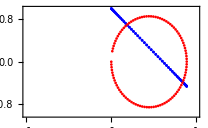

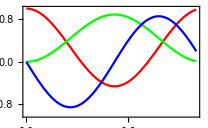

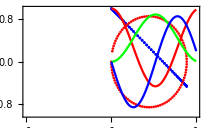

```mathematica
vn=0.95;
eqns={(s[1])'[z]==2 chi[vn]  s[3][z] ,(s[2])'[z]==-db[z] s[3][z],(s[3])'[z]==-2 chi[vn]  s[1][z]+db[z] s[2][z],s[1][zmin]==si[[1]],s[2][zmin]==si[[2]],s[3][zmin]==si[[3]]};
soln=NDSolve[eqns,{s[1],s[2],s[3]},{z,zmin,zmax}];
sv[z_]={s[1][z],s[2][z],s[3][z]}/.soln[[1]];
plt123z=ParametricPlot3D[sv[z],{z,zmin,zmax},PlotRange->{{-1.,1.},{-1.,1.},{-1.,1.}},DisplayFunction->Identity];
s2s1pts=Table[{sv[z][[2]],sv[z][[1]]},
{z,zmin,zmax,.01}];
s2s3pts=Table[{sv[z][[2]],sv[z][[3]]},
{z,zmin,zmax,.01}];
plt21z=ListPlot[s2s1pts,PlotRange->{{-1.,1.},{-1.,1.}},
PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity];
plt23z=ListPlot[s2s3pts,PlotRange->{{-1.,1.},{-1.,1.}},
PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity];
plt1z=Plot[sv[z][[1]],{z,zmin,zmax},PlotRange->{{zmin,zmax},{-1.,1.}},
PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity];
plt2z=Plot[sv[z][[2]],{z,zmin,zmax},PlotRange->{{zmin,zmax},{-1.,1.}},PlotStyle->RGBColor[0,1,0],DisplayFunction->Identity];
plt3z=Plot[sv[z][[3]],{z,zmin,zmax},PlotRange->{{zmin,zmax},{-1.,1.}},
PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity];
Show[pltsph, DisplayFunction->$DisplayFunction];
Show[{pltsph,plt123z},PlotLabel->eqns,PlotLegends->Automatic,DisplayFunction->$DisplayFunction, ViewPoint->viewPoint]
(*Export["dcSl",%,"tiff",ImageResolution->imres,ImageSize->{xsize,ysize}];*)
Show[plt21z,plt23z, Frame->True,PlotRangePadding->.2,DisplayFunction->$DisplayFunction ]
Show[plt1z,plt2z,plt3z,Frame->True,PlotRangePadding->.2, DisplayFunction->$DisplayFunction]
Show[{plt21z,plt23z},{plt1z,plt2z,plt3z},Frame->True,PlotRangePadding->.2, DisplayFunction->$DisplayFunction]
```

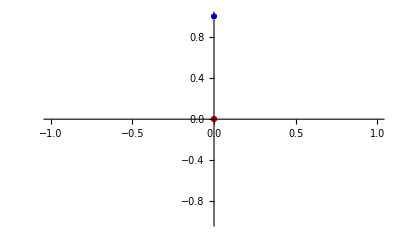
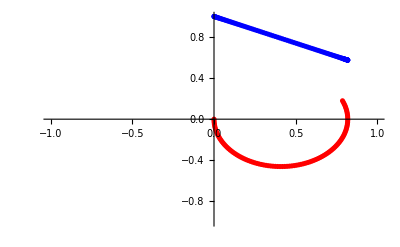
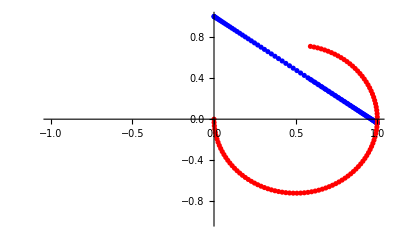
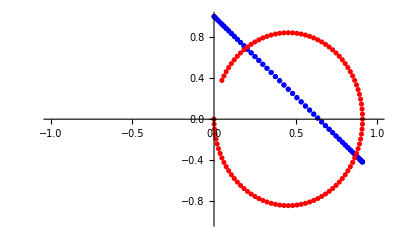
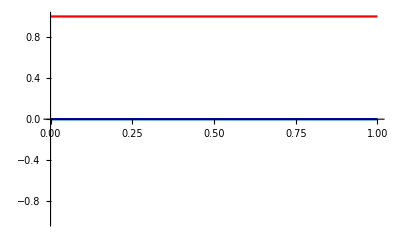
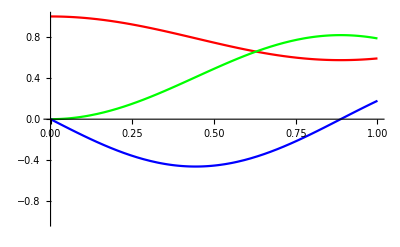
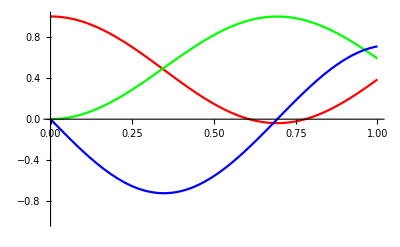
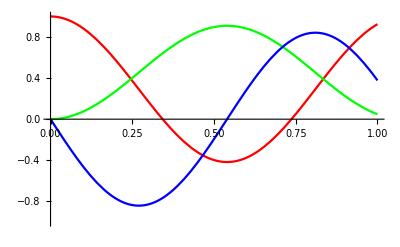
{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

-Graphics3D-

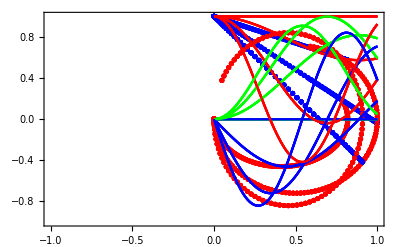

```mathematica
vnmax=1.;
vnmin=0.;
vninc=0.3;
(*Define a numerical solution*)
plts=Transpose[Table[Module[{},eqns={
(s[1])'[z]==2 chi[vn]  s[3][z] ,
(s[2])'[z]==-db[z] s[3][z],
(s[3])'[z]==-2 chi[vn]  s[1][z]+db[z] s[2][z],
s[1][zmin]==si[[1]],s[2][zmin]==si[[2]],s[3][zmin]==si[[3]]};
soln=NDSolve[eqns,{s[1],s[2],s[3]},{z,zmin,zmax}];
sv[z_]={s[1][z],s[2][z],s[3][z]}/.soln[[1]];
s2s1pts=Table[{sv[z][[2]],sv[z][[1]]},
{z,zmin,zmax,.01}];
s2s3pts=Table[{sv[z][[2]],sv[z][[3]]},
{z,zmin,zmax,.01}];

{ParametricPlot3D[sv[z],{z,zmin,zmax},PlotRange->{{-1.,1.},{-1.,1.},{-1.,1.}},
DisplayFunction->Identity, ViewPoint->{0,10,1}],

Show[ListPlot[s2s1pts,PlotRange->{{-1.,1.},{-1.,1.}},
PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity],ListPlot[s2s3pts,PlotRange->{{-1.,1.},{-1.,1.}},
PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity]],

Show[Plot[sv[z][[1]],{z,zmin,zmax},PlotRange->{{zmin,zmax},{-1.,1.}},
PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity],Plot[sv[z][[2]],{z,zmin,zmax},
PlotRange->{{zmin,zmax},{-1.,1.}},PlotStyle->RGBColor[0,1,0],
DisplayFunction->Identity],Plot[sv[z][[3]],{z,zmin,zmax},
PlotRange->{{zmin,zmax},{-1.,1.}},
PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity]]}],
{vn,vnmin,vnmax,vninc}]]

splts=Table[Show[Table[plts[[k]],{vn,vnmin,vnmax,vninc}], DisplayFunction->$DisplayFunction],{k,3}];
Show[vSphere,splts[[1]], Frame->True,ViewPoint-> viewPoint]
Show[splts[[2]],splts[[3]], Frame->True]

(*Export["dcSlvn",splts[[1]],"tiff",ImageResolution->imres,ImageSize->{xsize,ysize}];*)
```

{s(1)'(z)==5.4414 s(3)(z),s(2)'(z)==-π s(3)(z),s(3)'(z)==π s(2)(z)-5.4414 s(1)(z),s(1)(0)==1.,s(2)(0)==0,s(3)(0)==0.}

-Graphics3D-

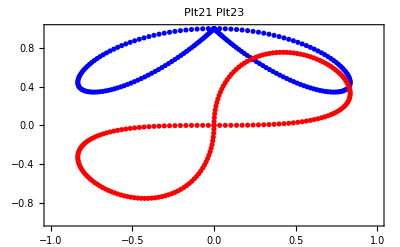

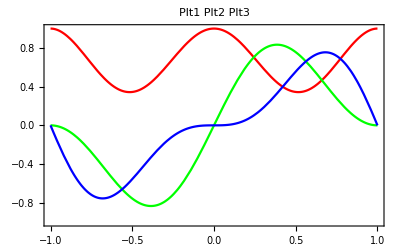

```mathematica
(*New Initial Conditions*)
vnmax=1.;
vnmin=-vnmax;
vninc=0.01;
svpts=Table[Module[{},eqns={(s[1])'[z]==2 chi[vn]  s[3][z] ,(s[2])'[z]==-db[z] s[3][z],(s[3])'[z]==-2 chi[vn]  s[1][z]+db[z] s[2][z],s[1][zmin]==si[[1]],s[2][zmin]==si[[2]],s[3][zmin]==si[[3]]};

soln=NDSolve[eqns,{s[1],s[2],s[3]},{z,zmin,zmax}];
sv[z_]={s[1][z],s[2][z],s[3][z]}/.soln[[1]];
{{vn,sv[zmax][[1]]},{vn,sv[zmax][[2]]},{vn,sv[zmax][[3]]},{vn,(1-sv[zmax][[2]])/2.}}],{vn,vnmin,vnmax,vninc}];
svp=Table[Interpolation[Transpose[svpts][[i]]],{i,3}];
trans=Interpolation[Transpose[svpts][[4]]];
TraditionalForm[eqns]
plt123=ParametricPlot3D[{svp[[1]][vn],
svp[[2]][vn],svp[[3]][vn]},{vn,vnmin,vnmax},PlotRange->{{-1.,1.},{-1.,1.},{-1.,1.}},DisplayFunction->Identity];
s2s1pts=Table[{svp[[2]][vn],svp[[1]][vn]},
{vn,vnmin,vnmax,vninc}];
s2s3pts=Table[{svp[[2]][vn],svp[[3]][vn]},
{vn,vnmin,vnmax,vninc}];
plt21=ListPlot[s2s1pts,PlotRange->{{-1.,1.},{-1.,1.}},
PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity];
plt23=ListPlot[s2s3pts,PlotRange->{{-1.,1.},{-1.,1.}},
PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity];
plt1=Plot[svp[[1]][vn],{vn,vnmin,vnmax},PlotRange->{{-1.,1.},{-1.,1.}},
PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity];
plt2=Plot[svp[[2]][vn],{vn,vnmin,vnmax},PlotRange->{{-1.,1.},{-1.,1.}},
PlotStyle->RGBColor[0,1,0],DisplayFunction->Identity];
plt3=Plot[svp[[3]][vn],{vn,vnmin,vnmax},PlotRange->{{-1.,1.},{-1.,1.}},PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity];
pltrans=Plot[trans[vn],{vn,vnmin,vnmax},PlotRange->{{-1.,1.},{0.,1.}},DisplayFunction->Identity];
Show[{pltsph, plt123} ,DisplayFunction->$DisplayFunction]
Show[plt123 ,DisplayFunction->$DisplayFunction];
(*Export["dcSv",%,"tiff",ImageResolution->imres,ImageSize->{xsize,ysize}];*)
Show[plt21,plt23, Frame->True, PlotLabel->"Plt21 Plt23",DisplayFunction->$DisplayFunction]
Show[plt1,plt2,plt3, Frame->True, PlotLabel->"Plt1 Plt2 Plt3", DisplayFunction->$DisplayFunction]
```

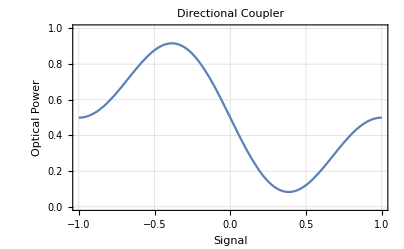

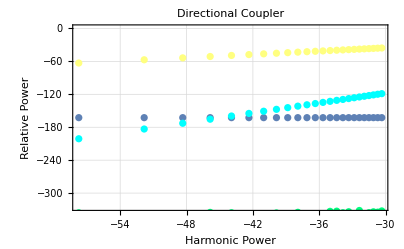

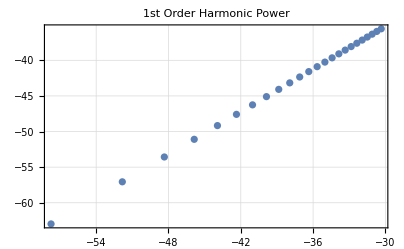

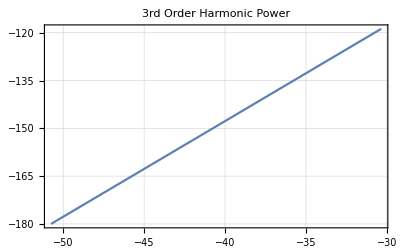

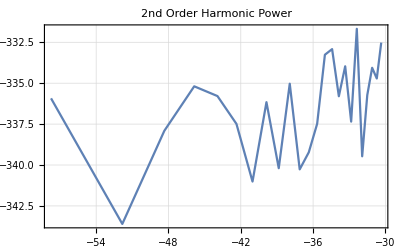

```mathematica
pin[amp_]:=0.5 amp^2/rm;
rm=50.;
ampmax=.01;
ampinc=ampmax/25.;
Tav=0.5;
Popt=0.1;
loss=0.1;
eta=0.7;
idc=Tav Popt loss eta;
eelec=1.6 10^(-19);
rd=50.;
Psn=10. (Log[10, 2. eelec idc 50.]+3.);
nf=Psn;
nfpts=Table[{10. (Log[10, pin[amp]]+3.),nf},{amp,ampinc + .00001,ampmax,ampinc}];
lpnf=ListPlot[nfpts, DisplayFunction-> Identity];

sfdrdata=Table[Table[{10. (Log[10,pin[amp]]+3.), Module[{},
ntp=1028;npr=1;
data=Table[trans[amp Sin[2 npr Pi n/ntp]],{n,0,ntp-1}];
tdata = 20. (Log[10,Abs[Fourier[data]]/(Sqrt[ntp]/2)+10^(-100)]);
tdata[[k+1]]]},{amp,ampinc+ .00001,ampmax,ampinc}],{k,5}];
lpfd=Table[ListPlot[sfdrdata[[k]],PlotStyle->{RGBColor[If[k==1,1,0],If[k==2,1,1],If[k==3,1,.5]], Thickness[If [k==1,.003, .01]]},

DisplayFunction->Identity],{k,3}];

Show[pltrans, DisplayFunction->$DisplayFunction,Frame->True,PlotLabel->"Directional Coupler",FrameLabel->{Signal,"Optical Power"},GridLines->Automatic]

(*Export["dctf",%,"tiff",ImageResolution->imres,ImageSize->{xsize,ysize}];*)
Show[lpnf,Table[lpfd[[k]],{k,3}], Frame->True,PlotLabel->"Directional Coupler",FrameLabel->{Harmonic Power,"Relative Power"},PlotLegends->{"1","2","3"},GridLines->Automatic,DisplayFunction->$DisplayFunction]
(*Export["dcfcs",%,"tiff",ImageResolution->imres,ImageSize->{xsize,ysize}];*)
ListPlot[sfdrdata[[1]], Frame->True,GridLines->Automatic,PlotRange->{0,-180}, PlotLabel->" 1st Order  Harmonic Power "]

ListPlot[sfdrdata[[3]], Frame->True,GridLines->Automatic,PlotRange->{0,-180},Joined->True, PlotLabel->" 3rd Order Harmonic Power "]
ListPlot[sfdrdata[[2]], Frame->True,GridLines->Automatic,Joined->True, PlotLabel->" 2nd Order Power "]
```